```mathematica
{t,t}.({t,Sin[t]}.RotationMatrix[π-π/4])
```

t (-t/(√2)-Sin[t]/(√2))+t (-t/(√2)+Sin[t]/(√2))

```mathematica
({t,Sin[t]}.RotationMatrix[π-π/4])
```

{-t/(√2)+Sin[t]/(√2),-t/(√2)-Sin[t]/(√2)}

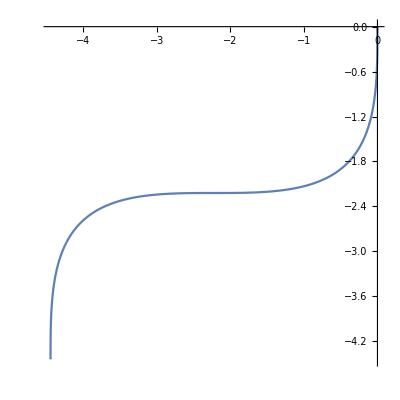

```mathematica
ParametricPlot[
{-t/(√2)+Sin[t]/(√2),-t/(√2)-Sin[t]/(√2)}
,{t,0,2π}]
```

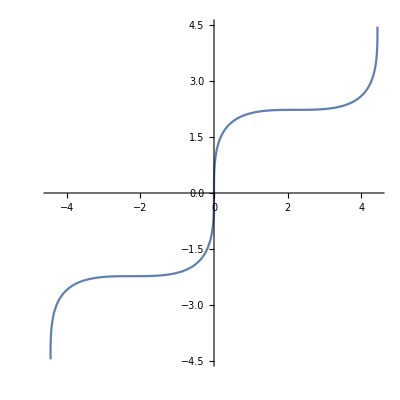

```mathematica
ParametricPlot[
{-t/(√2)+Sin[t]/(√2),-t/(√2)-Sin[t]/(√2)}
,{t,-2π,2π}]
```

```mathematica
({t,Sin[t]}.RotationMatrix[2π-π/4])
```

{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}

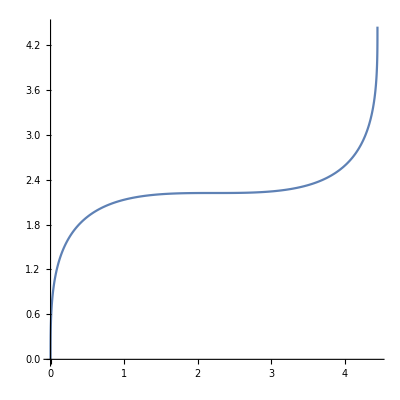

```mathematica
ParametricPlot[
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
,{t,0,2π}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]
,t∈Reals]
```

(√2)/(√(3+Cos[2 t]))

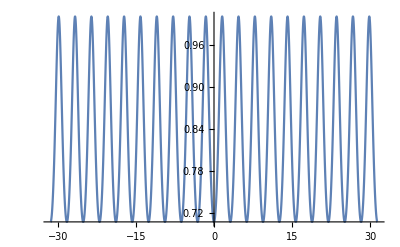

```mathematica
Plot[(√2)/(√(3+Cos[2 t])),{t,-10 π,10 π}]
```

```mathematica
(√2)/(√(3+Cos[2 t]))
```

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{a,b},t]==(√2)/(√(3+Cos[2 t]))
,{a,b,t}∈Reals]
```

False

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f'[t],g'[t]},t]==(√2)/(√(3+Cos[2 t]))
,{g'[t],f'[t],t}∈Reals]
```

(f''[t]+2 t g''[t])/(√(((1+4 t^2) (Abs[f''[t]]^2+Abs[g''[t]]^2))/(3+Cos[2 t])))==√2

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f'[t],g'[t]},t]==(√2)/(√(3+Cos[2 t]))
,{g'[t],f'[t],t,f''[t],g''[t]}∈Reals]
```

(f''[t]+2 t g''[t])/(√(((1+4 t^2) (f''[t]^2+g''[t]^2))/(3+Cos[2 t])))==√2

```mathematica
FullSimplify[
Normalize@D[{t,f[t]},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]==(√2)/(√(3+Cos[2 t]))
,t∈Reals]
```

(1-Cos[t]+(1+Cos[t]) f'[t])/(√((1+Abs[f'[t]]^2) (3+Cos[2 t])))==(√2)/(√(3+Cos[2 t]))

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f[t],g[t]},t]==(√2)/(√(3+Cos[2 t]))
,{g'[t],f'[t],t,f''[t],g''[t],f[t],g[t]}∈Reals]
```

(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(3+Cos[2 t])))==√2

```mathematica
DSolve[(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(3+Cos[2 t])))==√2,{f[t],g[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(3+Cos[2 t])))==√2,{f[t],g[t]},{t}]

```mathematica
DSolve[(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(3+Cos[2 t])))==√2,{f[t]},{t}]
```

{{f[t]→C[1]+(2 (3 K[1] g'[K[1]]+Cos[2 K[1]] K[1] g'[K[1]]-√(Cos[K[1]]^2 g'[K[1]]^2+8 Cos[K[1]]^2 K[1]^2 g'[K[1]]^2+16 Cos[K[1]]^2 K[1]^4 g'[K[1]]^2)))/(-1-Cos[2 K[1]]+8 K[1]^2)K[1]1t},{f[t]→C[1]+(2 (3 K[2] g'[K[2]]+Cos[2 K[2]] K[2] g'[K[2]]+√(Cos[K[2]]^2 g'[K[2]]^2+8 Cos[K[2]]^2 K[2]^2 g'[K[2]]^2+16 Cos[K[2]]^2 K[2]^4 g'[K[2]]^2)))/(-1-Cos[2 K[2]]+8 K[2]^2)K[2]1t}}

```mathematica
FullSimplify[
Normalize@D[{t,f[t]},t].Normalize@D[{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t]==(√2)/(√(3+Cos[2 t]))
,{t,f[t],f'[t]}∈Reals]
```

(1-Cos[t]+(1+Cos[t]) f'[t])/(√((3+Cos[2 t]) (1+f'[t]^2)))==(√2)/(√(3+Cos[2 t]))

```mathematica
DSolve[(1-Cos[t]+(1+Cos[t]) f'[t])/(√((3+Cos[2 t]) (1+f'[t]^2)))==(√2)/(√(3+Cos[2 t])),{f[t]},{t}]
```

{{f[t]→t+C[1]},{f[t]→t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]+C[1]}}

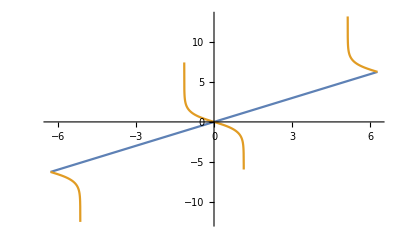

```mathematica
Plot[
{t,t-2 √(1+√2) ArcTan[Tan[t/2]/(√(1+√2))]-2 √(-1+√2) ArcTanh[Tan[t/2]/(√(-1+√2))]}
,{t,-2π,2π}]
```

```mathematica
f[x^2]==x^3
```

f[x^2]==x^3

```mathematica
Reduce[f[x^2]==x^3]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[f[x^2]==x^3]

```mathematica
ApplySides[f[x^2]==x^3,InverseFunction[f]]
```

ApplySides::eqin: f^(-1) should be an equation or an inequality.

ApplySides[f[x^2]==x^3,f^(-1)]

```mathematica
InverseFunction[f][f[x^2]]==InverseFunction[f][x^3]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

x^2==f^(-1)[x^3]

```mathematica
DSolve[{(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(3+Cos[2 t])))==√2,{f[t]},{t}]
```

```mathematica
Normalize@{t,Sin[t]}
```

{t/(√(Abs[t]^2+Abs[Sin[t]]^2)),Sin[t]/(√(Abs[t]^2+Abs[Sin[t]]^2))}

```mathematica
FullSimplify[Normalize@{t,Sin[t]},t∈Reals]
```

{t/(√(t^2+Sin[t]^2)),Sin[t]/(√(t^2+Sin[t]^2))}

```mathematica
FullSimplify[Norm@{t,Sin[t]},t∈Reals]
```

√(t^2+Sin[t]^2)

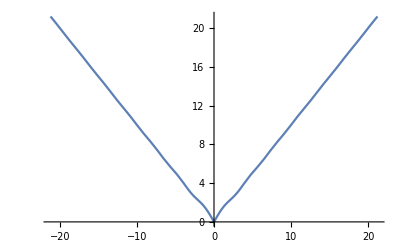

```mathematica
Plot[√(t^2+Sin[t]^2),{t,-21.205750411731103,21.205750411731103}]
```

```mathematica
√(t^2+Sin[t]^2)==1
```

√(t^2+Sin[t]^2)==1

```mathematica
Reduce[√(t^2+Sin[t]^2)==1]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[√(t^2+Sin[t]^2)==1]

```mathematica
{{f[t]->C[1]+(2 (3 K[1] g'[K[1]]+Cos[2 K[1]] K[1] g'[K[1]]-√(Cos[K[1]]^2 g'[K[1]]^2+8 Cos[K[1]]^2 K[1]^2 g'[K[1]]^2+16 Cos[K[1]]^2 K[1]^4 g'[K[1]]^2)))/(-1-Cos[2 K[1]]+8 K[1]^2)K[1]1t},{f[t]->C[1]+(2 (3 K[2] g'[K[2]]+Cos[2 K[2]] K[2] g'[K[2]]+√(Cos[K[2]]^2 g'[K[2]]^2+8 Cos[K[2]]^2 K[2]^2 g'[K[2]]^2+16 Cos[K[2]]^2 K[2]^4 g'[K[2]]^2)))/(-1-Cos[2 K[2]]+8 K[2]^2)K[2]1t}}
```

{{f[t]→C[1]+(2 (3 K[1] g'[K[1]]+Cos[2 K[1]] K[1] g'[K[1]]-√(Cos[K[1]]^2 g'[K[1]]^2+8 Cos[K[1]]^2 K[1]^2 g'[K[1]]^2+16 Cos[K[1]]^2 K[1]^4 g'[K[1]]^2)))/(-1-Cos[2 K[1]]+8 K[1]^2)K[1]1t},{f[t]→C[1]+(2 (3 K[2] g'[K[2]]+Cos[2 K[2]] K[2] g'[K[2]]+√(Cos[K[2]]^2 g'[K[2]]^2+8 Cos[K[2]]^2 K[2]^2 g'[K[2]]^2+16 Cos[K[2]]^2 K[2]^4 g'[K[2]]^2)))/(-1-Cos[2 K[2]]+8 K[2]^2)K[2]1t}}

```mathematica
Activate@(2 (3 K[2] g'[K[2]]+Cos[2 K[2]] K[2] g'[K[2]]+√(Cos[K[2]]^2 g'[K[2]]^2+8 Cos[K[2]]^2 K[2]^2 g'[K[2]]^2+16 Cos[K[2]]^2 K[2]^4 g'[K[2]]^2)))/(-1-Cos[2 K[2]]+8 K[2]^2)K[2]1t
```

∫_1^t (2 (3 K[2] g'[K[2]]+Cos[2 K[2]] K[2] g'[K[2]]+√(Cos[K[2]]^2 g'[K[2]]^2+8 Cos[K[2]]^2 K[2]^2 g'[K[2]]^2+16 Cos[K[2]]^2 K[2]^4 g'[K[2]]^2)))/(-1-Cos[2 K[2]]+8 K[2]^2)ⅆK[2]

```mathematica
∫_1^t (2 (3 K[2] g'[K[2]]+Cos[2 K[2]] K[2] g'[K[2]]+√(Cos[K[2]]^2 g'[K[2]]^2+8 Cos[K[2]]^2 K[2]^2 g'[K[2]]^2+16 Cos[K[2]]^2 K[2]^4 g'[K[2]]^2)))/(-1-Cos[2 K[2]]+8 K[2]^2)ⅆK[2]/.K[2]->x
```

∫_1^t (2 (3 x g'[x]+x Cos[2 x] g'[x]+√(Cos[x]^2 g'[x]^2+8 x^2 Cos[x]^2 g'[x]^2+16 x^4 Cos[x]^2 g'[x]^2)))/(-1+8 x^2-Cos[2 x])ⅆx

```mathematica
Dt[∫_1^t (2 (3 x g'[x]+x Cos[2 x] g'[x]+√(Cos[x]^2 g'[x]^2+8 x^2 Cos[x]^2 g'[x]^2+16 x^4 Cos[x]^2 g'[x]^2)))/(-1+8 x^2-Cos[2 x])ⅆx]
```

(2 Dt[t] (3 t g'[t]+t Cos[2 t] g'[t]+√(Cos[t]^2 g'[t]^2+8 t^2 Cos[t]^2 g'[t]^2+16 t^4 Cos[t]^2 g'[t]^2)))/(-1+8 t^2-Cos[2 t])

```mathematica
{t,Cos[t]}.RotationMatrix[π-π/4]
```

{-t/(√2)+Cos[t]/(√2),-t/(√2)-Cos[t]/(√2)}

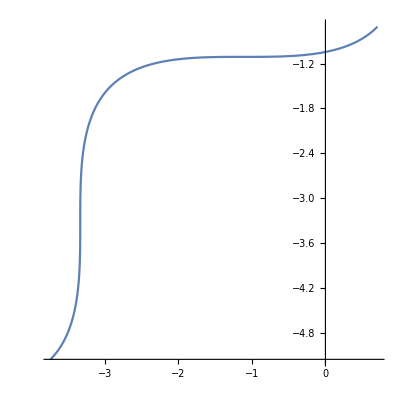

```mathematica
ParametricPlot[
{-t/(√2)+Cos[t]/(√2),-t/(√2)-Cos[t]/(√2)}
,{t,0,2π}]
```

```mathematica
{t,Cos[t]}.RotationMatrix[2π-π/4]
```

{t/(√2)-Cos[t]/(√2),t/(√2)+Cos[t]/(√2)}

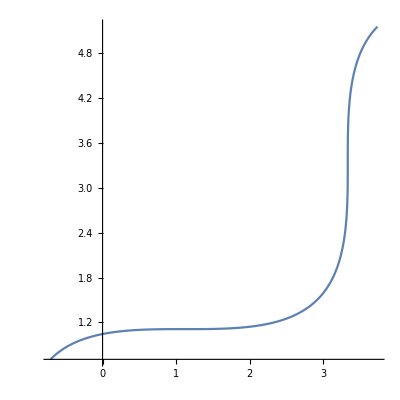

```mathematica
ParametricPlot[
{t/(√2)-Cos[t]/(√2),t/(√2)+Cos[t]/(√2)}
,{t,0,2π}]
```

```mathematica
[{t,Cos[t]}.RotationMatrix[θ]
```

```mathematica
Manipulate[
ParametricPlot[
{t,Cos[t]}.RotationMatrix[θ]
,{t,0,2π}]
,{θ,0,2π}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t},t].Normalize@D[{t/(√2)-Cos[t]/(√2),t/(√2)+Cos[t]/(√2)},t]
,{t,f[t],f'[t]}∈Reals]
```

1/(√(1+Sin[t]^2))

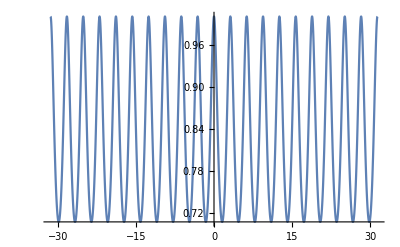

```mathematica
Plot[1/(√(1+Sin[t]^2)),{t,-10 π,10 π}]
```

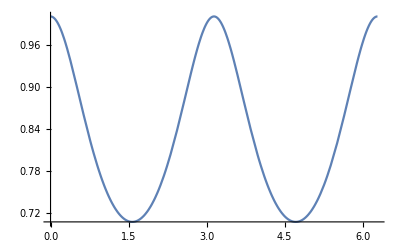

```mathematica
Plot[1/(√(1+Sin[t]^2)),{t,0,2 π}]
```

```mathematica
Integrate[1/(√(1+Sin[t]^2)),t]
```

EllipticF[t,-1]

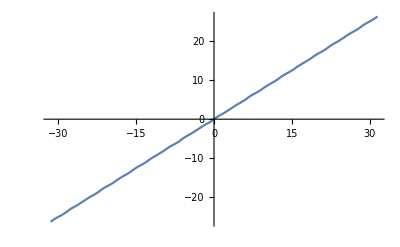

```mathematica
Plot[EllipticF[t,-1],{t,-31.464690651505435,31.464690651505435}]
```

```mathematica
FullSimplify[
Normalize@D[{t,t^2},t].Normalize@D[{f[t],g[t]},t]==1/(√(1+Sin[t]^2))
,{t,f[t],f'[t],g[t],g'[t]}∈Reals]
```

(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(1+Sin[t]^2)))==1

```mathematica
DSolve[(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(1+Sin[t]^2)))==1,{f[t],g[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(1+Sin[t]^2)))==1,{f[t],g[t]},{t}]

```mathematica
DSolve[(f'[t]+2 t g'[t])/(√(((1+4 t^2) (f'[t]^2+g'[t]^2))/(1+Sin[t]^2)))==1,{f[t]},{t}]
```

{{f[t]→C[1]+(2 (3 K[1] g'[K[1]]-Cos[2 K[1]] K[1] g'[K[1]]-√(Sin[K[1]]^2 g'[K[1]]^2+8 K[1]^2 Sin[K[1]]^2 g'[K[1]]^2+16 K[1]^4 Sin[K[1]]^2 g'[K[1]]^2)))/(-1+Cos[2 K[1]]+8 K[1]^2)K[1]1t},{f[t]→C[1]+(2 (3 K[2] g'[K[2]]-Cos[2 K[2]] K[2] g'[K[2]]+√(Sin[K[2]]^2 g'[K[2]]^2+8 K[2]^2 Sin[K[2]]^2 g'[K[2]]^2+16 K[2]^4 Sin[K[2]]^2 g'[K[2]]^2)))/(-1+Cos[2 K[2]]+8 K[2]^2)K[2]1t}}

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcTan[2]
```

ArcTan[2]

```mathematica
N@ArcTan[2]
```

1.10715

```mathematica
FullSimplify[{t,Cos[t]}.RotationMatrix[ArcTan[2]],t∈Reals]
```

{(t+2 Cos[t])/(√5),(-2 t+Cos[t])/(√5)}

```mathematica
FullSimplify[{t,Cos[t]}.RotationMatrix[ArcTan[θ]],t∈Reals]
```

{(t+θ Cos[t])/(√(1+θ^2)),(-t θ+Cos[t])/(√(1+θ^2))}

```mathematica
{(t+θ Cos[t])/(√(1+θ^2)),(-t θ+Cos[t])/(√(1+θ^2))}
```

```mathematica
FullSimplify[
Normalize@D[{t,2t},t].Normalize@D[{(t+θ Cos[t])/(√(1+θ^2)),(-t θ+Cos[t])/(√(1+θ^2))},t]
,{t,f[t],f'[t],g[t],g'[t]}∈Reals]
```

(1-2 θ-(2+θ) Sin[t])/(√5 √((1+Abs[θ]^2) Sign[1+θ^2] (1+Sin[t]^2)))

```mathematica
FullSimplify[
Normalize@D[{t,θ t},t].Normalize@D[{(t+θ Cos[t])/(√(1+θ^2)),(-t θ+Cos[t])/(√(1+θ^2))},t]
,{t,f[t],f'[t],g[t],g'[t]}∈Reals]
```

-(-1+θ^2+2 θ Sin[t])/((1+Abs[θ]^2) √(Sign[1+θ^2] (1+Sin[t]^2)))

```mathematica
FullSimplify[
Normalize@D[{t,θ t},t].Normalize@D[{(t+θ Cos[t])/(√(1+θ^2)),(-t θ+Cos[t])/(√(1+θ^2))},t]
,{t,f[t],f'[t],g[t],g'[t],θ}∈Reals]
```

(1-θ^2-2 θ Sin[t])/((1+θ^2) √(1+Sin[t]^2))

```mathematica
(1-θ^2-2 θ Sin[t])/((1+θ^2) √(1+Sin[t]^2))/.θ->ArcTan[1]
```

(1-π^2/16-1/2 π Sin[t])/((1+π^2/16) √(1+Sin[t]^2))

```mathematica
FullSimplify[(1-π^2/16-1/2 π Sin[t])/((1+π^2/16) √(1+Sin[t]^2))]
```

(16-π^2-8 π Sin[t])/((16+π^2) √(1+Sin[t]^2))

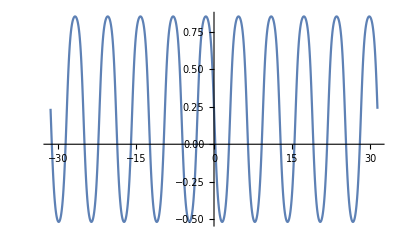

```mathematica
Plot[(16-π^2-8 π Sin[t])/((16+π^2) √(1+Sin[t]^2)),{t,-10 π,10 π}]
```

```mathematica
Dt[Sin[t]]
```

Cos[t] Dt[t]

```mathematica
Dt[Dt[Sin[t]]]
```

Cos[t] Dt[Dt[t]]-Dt[t]^2 Sin[t]

```mathematica
Cos[t] Dt[Dt[t]]-Dt[t]^2 Sin[t]/.Dt[t]->1
```

-Sin[t]

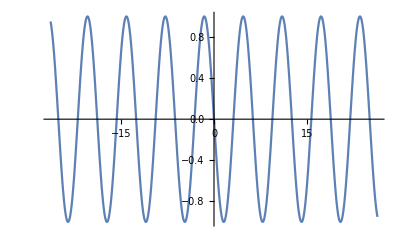

```mathematica
Plot[-Sin[t],{t,-26.389378290154262,26.389378290154262}]
```

```mathematica
f[Sin[t]]->0
```

f[Sin[t]]→0

```mathematica
f:[Sin[t]]->0
```

```mathematica
f:Sin[t]->0
```

f:Sin[t]→0

```mathematica
f:Sin[t]/.f:Sin[t]->0
```

f:0

```mathematica
(f[t]==f[t-α])->f[t+α]==f[t]
```

f[t]==f[t-α]→f[t+α]==f[t]

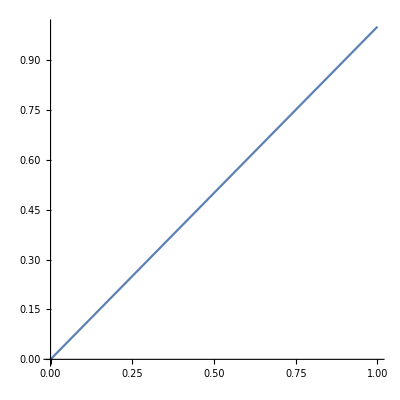

```mathematica
ParametricPlot[
{t,t}
,{t,0,1}]
```

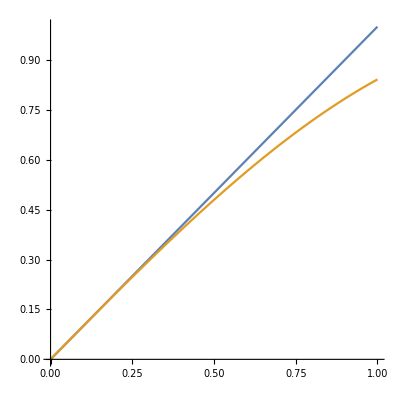

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]}
},{t,0,1}]
```

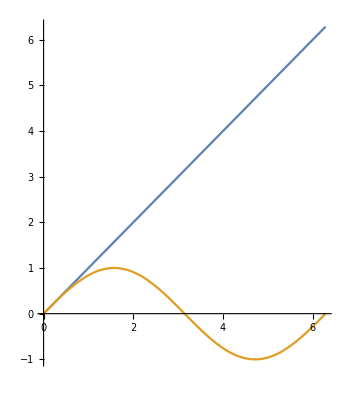

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]}
},{t,0,2π}]
```

```mathematica
{1,0}
```

{1,0}

```mathematica
{0,1}
```

{0,1}

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]}
},{t,0,2π}]
```

```mathematica
Sin[t]/(-f'[t])
```

-Sin[t]/f'[t]

```mathematica
{t-Sin[t],t+Sin[t]}
```

{t-Sin[t],t+Sin[t]}

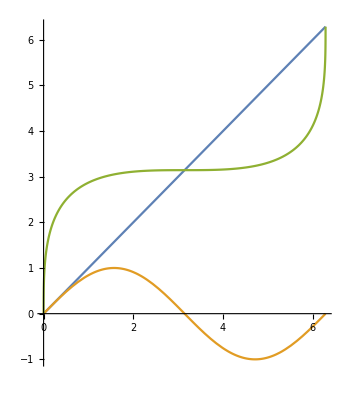

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]}
},{t,0,2π}]
```

```mathematica
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
```

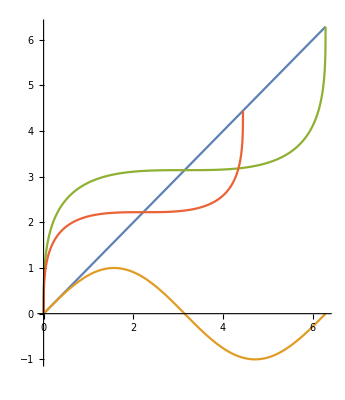

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,0,2π}]
```

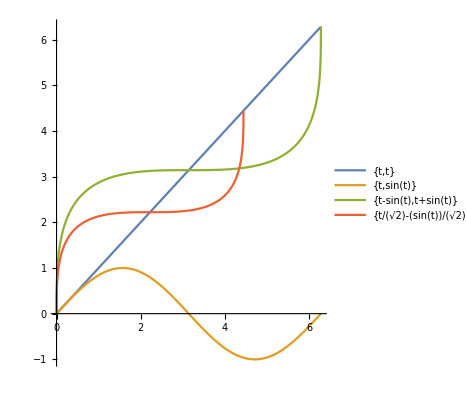

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,0,2π},PlotLegends->"Expressions"]
```

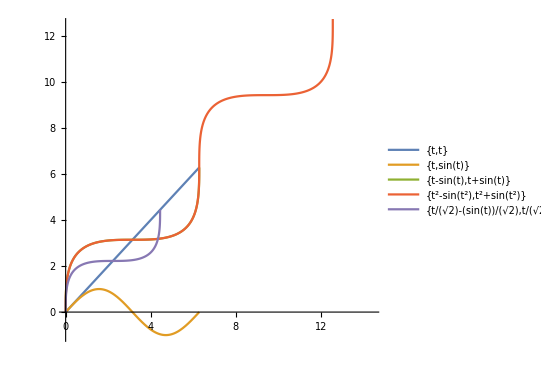

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{t^2-Sin[t^2],t^2+Sin[t^2]},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,0,2π},PlotLegends->"Expressions"]
```

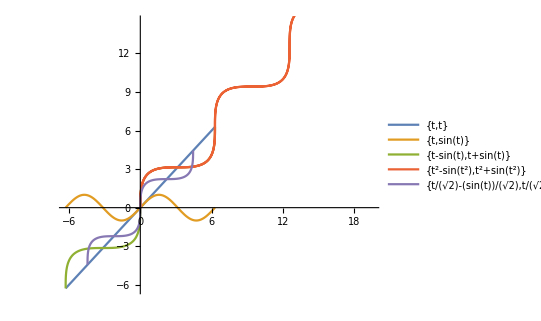

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{t^2-Sin[t^2],t^2+Sin[t^2]},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,-2π,2π},PlotLegends->"Expressions"]
```

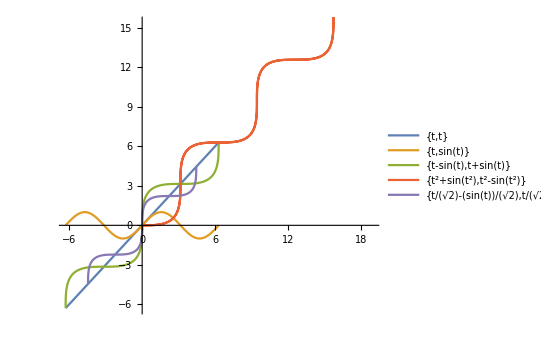

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{t^2+Sin[t^2],t^2-Sin[t^2]},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,-2π,2π},PlotLegends->"Expressions"]
```

```mathematica
{t-Sin[t],t+Sin[t]}
```

{t-Sin[t],t+Sin[t]}

```mathematica
∫_0^(2π) Norm[{t-Sin[t],t+Sin[t]}]ⅆt
```

∫_0^(2 π) √(Abs[t-Sin[t]]^2+Abs[t+Sin[t]]^2)ⅆt

```mathematica
∫_0^1 √(1+1)ⅆx
```

√2

```mathematica
∫_0^1 √(1+4x x)ⅆx
```

1/4 (2 √5+ArcSinh[2])

```mathematica
N[1/4 (2 √5+ArcSinh[2])]
```

1.47894

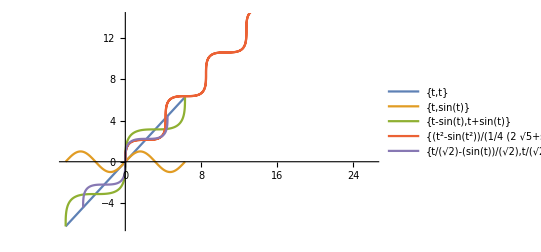

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{(t^2-Sin[t^2])/(1/4 (2 √5+ArcSinh[2])),(t^2+Sin[t^2])/(1/4 (2 √5+ArcSinh[2]))},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,-2π,2π},PlotLegends->"Expressions"]
```

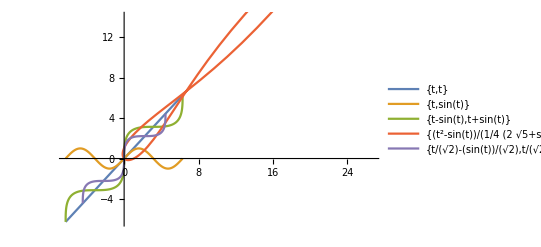

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{(t^2-Sin[t])/(1/4 (2 √5+ArcSinh[2])),(t^2+Sin[t])/(1/4 (2 √5+ArcSinh[2]))},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,-2π,2π},PlotLegends->"Expressions"]
```

```mathematica
ParametricPlot[{
{t,t},
{t,Sin[t]},
{t-Sin[t],t+Sin[t]},
{(t^2-Sin[t])/(1/4 (2 √5+ArcSinh[2])),(t^2+Sin[t])/(1/4 (2 √5+ArcSinh[2]))},
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
},{t,-2π,2π},PlotLegends->"Expressions"]
```

```mathematica
{(f[t]-Sin[t])/(∫_0^1 √(1+f'[t])ⅆt),(f[t]+Sin[t])/(∫_0^1 √(1+f'[t])ⅆt)}
```

{(f[t]-Sin[t])/(∫_0^1 √(1+f'[t])ⅆt),(f[t]+Sin[t])/(∫_0^1 √(1+f'[t])ⅆt)}

```mathematica
With[{f=Identity},{(f[t]-Sin[t])/(∫_0^1 √(1+f'[t])ⅆt),(f[t]+Sin[t])/(∫_0^1 √(1+f'[t])ⅆt)}]
```

{(t-Sin[t])/(√2),(t+Sin[t])/(√2)}

```mathematica
With[{f=Function[t,t t]},{(f[t]-Sin[t])/(∫_0^1 √(1+f'[t])ⅆt),(f[t]+Sin[t])/(∫_0^1 √(1+f'[t])ⅆt)}]
```

{(t^2-Sin[t])/(-1/3+√3),(t^2+Sin[t])/(-1/3+√3)}

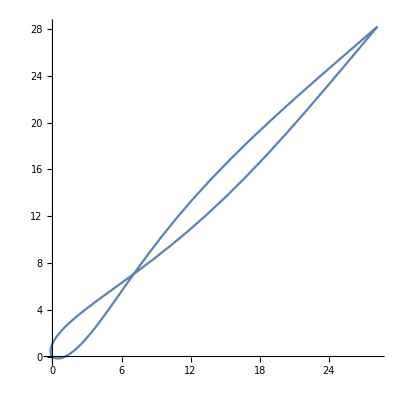

```mathematica
ParametricPlot[{
{(t^2-Sin[t])/(-1/3+√3),(t^2+Sin[t])/(-1/3+√3)}
},{t,-2π,2π},PlotLegends->"Expressions"]
```

```mathematica
RSolve[{a[n]==2a[n-1],a[0]==1},{a[n]},n]
```

{{a[n]→2^n}}

```mathematica
Dt[Power[2,n]]
```

2^n Dt[n] Log[2]

```mathematica
With[{f=Function[t,t t t]},{(f[t]-Sin[t])/(∫_0^1 √(1+f'[t])ⅆt),(f[t]+Sin[t])/(∫_0^1 √(1+f'[t])ⅆt)}]
```

{(6 (t^3-Sin[t]))/(6+√3 ArcSinh[√3]),(6 (t^3+Sin[t]))/(6+√3 ArcSinh[√3])}

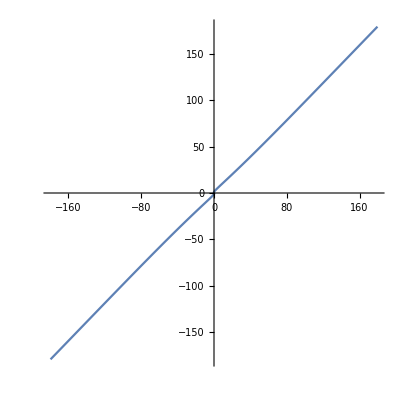

```mathematica
ParametricPlot[{
{(6 (t^3-Sin[t]))/(6+√3 ArcSinh[√3]),(6 (t^3+Sin[t]))/(6+√3 ArcSinh[√3])}
},{t,-2π,2π},PlotLegends->"Expressions"]
```